```mathematica
ODVOD FUNKCIJE
```

```mathematica
Odvod funkcije -  v določeni točki je limita diferenčnega kvocienta Δy/Δx, ko gre Δx proti nič.
```

```mathematica
Geometrijski pomen  odvoda - vrednost odvoda funkcije v X0 je enaka smernemu koeficientu tangente na graf funkcije v točki z absciso X0.
```

```mathematica
Kot pod katerim seka krivulja seka os x - je enak naklonskemu kotu tangente na krivuljo v presečišču z osjo x.
```

```mathematica
Kot pod katerm se sekata krivulji - je enak kotu med tangentama na obe krivulji v njumen presečišču.
```

```mathematica
Pravila za odvajanje :
```

```mathematica
Odvod konstante funkcije                  (c') = 0
```

```mathematica
Odvod potenčne funkcije                    (x^n)' = n * x^(n - 1)
```

```mathematica
Odvod vsote funkcij                             (f + g)' = f' + g'
```

```mathematica
Odvod zmnožka dveh funkcij               (f * g)'= f'* g + f*g'
```

```mathematica
Odvod zmnoška funkcije s konstantno funkcijo      (c*f)' = c* f'
```

```mathematica
Odvod količnika dveh funkcij(f/g)' = (f' * g - f * g')/g^2
```

```mathematica
1.NALOGA
```

```mathematica
f(x) = (2x + 1)/(x^2+6x + 5)
```

```mathematica
Določi ničle, pole
```

```mathematica
ničle
```

```mathematica
Solve[2x +1 == 0, x]
```

{{x→-1/2}}

```mathematica
pol
```

```mathematica
Solve[x^2+6x +5 ==0,x]
```

{{x→-5},{x→-1}}

```mathematica
2.NALOGA
```

```mathematica
določi minimumin maksimum  g(x) = x^3 -5x +6, D (-3,3)
```

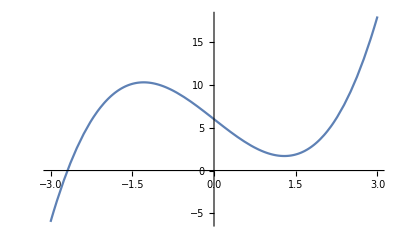

```mathematica
Plot[g, {x, -3,3}]
```

```mathematica
g = x^3 -5x + 6
D[g,x]
```

6-5 x+x^3

-5+3 x^2

```mathematica
Solve[-5 +3 x^2==0, x]
```

{{x→-√(5/3)},{x→√(5/3)}}

```mathematica
ReplaceAll[g,{x->-√(5/3)}]
```

6+(10 √(5/3))/3

```mathematica
ReplaceAll[g,{x->√(5/3)}]
```

6-(10 √(5/3))/3

```mathematica
{√(5/3), 6-(10 √(5/3))/3}
```

```mathematica
{-√(5/3), 6+(10 √(5/3))/3}
```

```mathematica
D[D[g,x],x]   (*naredili smo drugi odvod*)
```

6 x

```mathematica
ReplaceAll[6x, x-> -√(5/3)]
```

-2 √15

```mathematica
ReplaceAll[6x, x -> √(5/3)]
```

2 √15

```mathematica
ReplaceAll[g,x -> -3] (*dobili smo točko (-3, -6)*)
```

-6

```mathematica
ReplaceAll[g,x -> 3] (*dobili smo točko 3, 18*)
```

18

```mathematica
(*primerjamo vrednosti *)
```

```mathematica
-6 < 6-(10 √(5/3))/3
```

True

```mathematica
18> 6+(10 √(5/3))/3
```

True

```mathematica
3.NALOGA
```

```mathematica
Poišči min in max  h(x) = x + 2sin(x) na intervalu [0,2π]
```

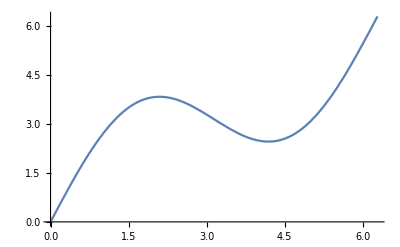

```mathematica
h[x_]:= x +2Sin[x]
Plot[h[x], {x, 0, 2Pi}]
```

```mathematica
Solve[h'[x]== 0, x]
```

{{x→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ]}}

```mathematica
Reduce[h'[x]== 0 && 0 ≤ x ≤ 2Pi ,x]
```

x==(2 π)/3||x==(4 π)/3

```mathematica
FindRoot[h'[x]== 0, {x, 0, 2Pi}]
```

{x→4.18879}

```mathematica
rezultat  = {0, 2Pi / 3, 4Pi /3, 2Pi}
```

{0,(2 π)/3,(4 π)/3,2 π}

```mathematica
h[rezultat]
```

{0,√3+(2 π)/3,-√3+(4 π)/3,2 π}

```mathematica
N[h[rezultat]]
```

{0.,3.82645,2.45674,6.28319}